# Homework - 3 [CSCI 561 Artificial Intelligence]

## CIFAR-100 Dataset

## Problem Statement

To analyze the dataset to understand various supervised machine learning techniques. To understand various pre-processing techniques that could be done on an dataset consisting of image so as to train the machine appropriately.

## Dataset Description

CIFAR-100 is a labeled subsets of 80 million tiny color images downsized to 32x32 dataset.It has 100 classes containing 600 images each. There are 500 training images and 100 testing images per class. The 100 classes in the CIFAR-100 are grouped into 20 superclasses. The “TrainingDataSet” consists of label (Fine Label) and a superclass (Coarse Label).

```mathematica
dataObject = ResourceObject["CIFAR-100"]
```

ResourceObject[…]

Now, to extract the training and test data from the dataObject using ResourceData.

```mathematica
trainingData=ResourceData[dataObject,"TrainingData"];
testData = ResourceData[dataObject,"TestData"];
```

To view the number of classes present in our training and test dataset, we perform the below function:

```mathematica
classes = Union @Values[trainingData]
```

{apple,aquarium fish,baby,bear,beaver,bed,bee,beetle,bicycle,bottle,bowl,boy,bridge,bus,butterfly,camel,can,castle,caterpillar,cattle,chair,chimpanzee,clock,cloud,cockroach,computer keyboard,couch,crab,crocodile,cup,dinosaur,dolphin,elephant,flatfish,forest,fox,girl,hamster,house,kangaroo,lamp,lawn-mower,leopard,lion,lizard,lobster,man,maple tree,motorcycle,mountain,mouse,mushroom,oak tree,orange,orchid,otter,palm tree,pear,pickup truck,pine tree,plain,plate,poppy,porcupine,possum,rabbit,raccoon,ray,road,rocket,rose,sea,seal,shark,shrew,skunk,skyscraper,snail,snake,spider,squirrel,streetcar,sunflower,sweet pepper,table,tank,telephone,television,tiger,tractor,train,trout,tulip,turtle,wardrobe,whale,willow tree,wolf,woman,worm}

Since I am using just the trainingData and not the trainingDataSet, therefore only considering the Fine Labels and not both Fine and Coarse.

## Supervised Learning

With the above dataset, I have performed:

NEURAL NETWORK

DECISION TREE - RANDOM FOREST

SUPPORT VECTOR MACHINE

In order to train the machine to predict which class an image belongs to, certain set of preprocessing needs to be done.

### Pre-Processing:

Extracting only images from the dataset can be done by using “Keys” function, to understand and manipulate images.

```mathematica
trainingImages = Keys[RandomSample[trainingData,5]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The pre-processing technique that I have used is image subtraction on gaussian filtered images.

Reducing the dataset size of the training images to 100 tiny images per class giving a training dataset of 10000 tiny images.The below steps need to followed to achieve the same, this helps in reducing the execution time to train and pre-process the training set.

```mathematica
reducedTrainingData={};
```

```mathematica
For[i=1,i≤50000,i+=500,reducedTrainingData=Join[reducedTrainingData,RandomSample[Take[trainingData,{i,i+499}],100]]];
```

The output of this gives a list of list of each class therefore need to flatten the list.

```mathematica
modifiedTrainingData=Flatten[reducedTrainingData];
```

Reducing the dataset size of the test images to 50 tiny images per class giving the test data to be 5000 tiny images.

```mathematica
reducedTestData = {};
```

```mathematica
For[i=1,i≤10000,i+=100,reducedTestData=Join[reducedTestData,RandomSample[Take[testData,{i,i+99}],30]]];
```

The output of this gives a list of list of each class therefore need to flatten the list.

```mathematica
modifiedTestData = Flatten[reducedTestData];
```

Gaussian Filtered :

Gaussian filtering is used to blur images and remove noise.

Removes the high-frequency components from the image, therefore giving us a smoothened version of the image.

Works with arbitrary 2D and 3D images, operating separately on each channel, as well as data arrays of any rank.

The wolfram language gives us a predefined function: GaussianFilter[Image,Kernel with radius]

Image Subtracted :

It is a process whereby the digital numeric value of one pixel or whole image is subtracted from another image.

Here I am subtracting a gaussian filtered image from all the pixels in the original image.

The image returned has the same dimensions as original image.

The wolfram language provides a predefined function: ImageSubtract[Image1, Image2]. I am passing the gaussian filtered image to the ImageSubtract function.

Image Add :

Typically gives an image with the same underlying data type as image, clipping or truncating values if necessary.

The image returned has the same dimensions as image.

The output of this will be a sharpened version of the original image.

The wolfram language provides a predefined function: ImageAdd[image1,image2]. I am passing the image subtracted image as the second parameter the ImageAdd function.

The below function has been implemented on both the test and the training data to improve accuracy.

```mathematica
preProcessingFunction[x_] := ImageAdd[x, ImageSubtract[x, GaussianFilter[x,2]]];
```

Executing the above function for Training and Test data

```mathematica
preProcessedTrainingData = Normal[KeyMap[preProcessingFunction,<|modifiedTrainingData|>]];
```

```mathematica
preProcessedTestData =Normal[KeyMap[preProcessingFunction,<|modifiedTestData|>]];
```

Feature Extraction[Built-In Mathematica Function]:

This can be used on many types of data, including numerical, textual, sounds, and images, as well as a combinations of these.

The result of this function returns a FeatureExtractorFunction that can be applied to specific dataset which is given as input to classifier.

This function basically performs the “Numerical Vector” method i.e it will convert dataset to numeric vectors, impute missing data, and reduce the dimension using another built in function call DimensionReduction.

Dimension Reduction:

This function automatically chooses an appropriate dimension for the target approximating manifold.

This function reduces the dimension of each image in the dataset based on some approximation.The output of this function leads to dimensionally reduced set of images.

Applying FeatureExtraction to the images in the preprocessed data. This can be done using the “Keys” function and then using the result of this function as an input to the “FeatureExtractor”.

```mathematica
preProcessedTrainingImages = Keys[preProcessedTrainingData];
```

```mathematica
featureExtractedData = FeatureExtraction[preProcessedTrainingImages]
```

FeatureExtractorFunction[…]

### Classification Methods:

#### Decision Trees:

A decision tree is a tree in which each internal (non-leaf) node contains an input feature. The arcs coming from a node labeled with a feature are labeled with each of the possible values of the feature. Each leaf of the tree is labeled with a class or a probability distribution over the classes.To classify an example, filter it down the tree, as follows. For each feature encountered in the tree, the arc corresponding to the value is followed. When a leaf is reached, the classification corresponding to that leaf is returned.

Random Forest:

It is an extension of decision trees in which multiple trees are grown as opposed to a single tree.

The reason this method was chosen:

It runs efficiently on large data bases

It can handle thousands of input variables without variable deletion

generated forests can be saved for future use on other data

For this dataset, I would be running the random forest method using the built in classify function with the performance goal to be Training Speed so as to minimize the amount of time used to train the classifier.

```mathematica
randomForest = Classify[preProcessedTrainingData,Method->"RandomForest",FeatureExtractor->featureExtractedData]
```

ClassifierFunction[…]

#### Neural Network:

An Artificial Neural Network (ANN) is an information processing paradigm that is inspired by the way biological nervous systems, such as the brain, process information.It is composed of a large number of highly interconnected processing elements (neurones) working in unison to solve specific problems. They learn by example. It is used for data classification, through a learning process.

They have the ability to derive meaning from complicated or imprecise data, can be used to extract patterns and detect trends that are too complex to be noticed by either humans or other computer techniques. A trained neural network can be thought of as an “expert” in the category of information it has been given to analyse. This expert can then be used to provide projections given new situations of interest and answer “what if” questions.

For this dataset, I would be running the neural network method using the built in classify function with the performance goal to be Training Speed so as to minimize the amount of time used to train the classifier.

```mathematica
neuralNet = Classify[preProcessedTrainingData,Method->"NeuralNetwork",FeatureExtractor->featureExtractedData]
```

ClassifierFunction[…]

#### Support Vector Machine:

A support vector machine constructs a hyperplane or set of hyperplanes in a high- or infinite-dimensional space, which can be used for classification, regression.

Support vectors are the data points nearest to the hyperplane, the points of a data set that, if removed, would alter the position of the dividing hyperplane. Because of this, they can be considered the critical elements of a data set.

A hyperplane as a line that linearly separates and classifies a set of data.Intuitively, the further from the hyperplane our data points lie, the more confident we are that they have been correctly classified.

I chose Support Vector Machine as remarkable recognition rates achieved in various experiments indicate that Support Vector Machines are well-suited for aspect-based recognition and color-based classification. I have implemented this by running the support vector machine method using the built in classify function with the performance goal to be Training Speed so as to minimize the amount of time used to train the classifier.

```mathematica
supportVector = Classify[preProcessedTrainingData, Method->"SupportVectorMachine",FeatureExtractor->featureExtractedData]
```

ClassifierFunction[…]

## Findings

I tried various preprocessing techniques to come up with the best possible pre-processed data to input to the classifier function. The below are my findings with the accuracy for each type of pre-processing technique.

#### Convolution Neural Network:

No PreProcessing - 36.30%

ImageSubtract with GaussianFilter - 38.40%

LaplacianGaussianFilter - 35.50%

EdgeDetect - 19.10%

ImageResize - 17.90%

TotalVariationFilter with deviation 0.25 - 36.95%

#### Artificial Neural Network:

FeatureExtractor with Dimension Reduction - 58.50%

ImageSubtract with GaussianFilter - 62.85%

#### Random Forest:

FeatureExtractor with Dimension Reduction - 44%

ImageSubtract with GaussianFilter - 45.07%

TotalVariationFilter with deviation 0.25 - 40.15%

ImageAdd, ImageSubtract, GradientFilter + FeatureExtraction - 6.80%

After going through the above results, as Image Add on Image Subtracted Gaussian Image gave the best accuracy in all the above cases. I used this technique on the raw data and then ran the built in feature extractor on the preprocessed data to get the best results. The above findings were performed on the entire training dataset and test dataset.The results section describes accuracy only for the modified sampled training and test dataset.

## Results

The below set of code is implemented to show the accuracy, precision/recall and ROC curve for each of the methods described in the Methods Section of the notebook.

This is implemented using the built-in ClassifierMeasurement function. This specifies that the classifier should use the options opts when applied to the test set against the trained data set.

#### Decision Tree

The ClassifierMeasurement function for decision trees:

```mathematica
decisionMeasure = ClassifierMeasurements[randomForest,preProcessedTestData]
```

ClassifierMeasurementsObject[…]

Accuracy of the classifier:

```mathematica
decisionMeasure["Accuracy"]
```

0.469

Precision of each class in the dataset:

```mathematica
decisionMeasure["Precision"]
```

<|apple→0.642857,aquarium fish→0.35443,baby→0.433333,bear→0.142857,beaver→0.0909091,bed→0.375,bee→0.339623,beetle→0.424242,bicycle→0.375,bottle→0.448276,bowl→0.391304,boy→0.340426,bridge→0.357143,bus→0.313725,butterfly→0.44,camel→0.5,can→0.55,castle→0.461538,caterpillar→0.378788,cattle→0.5,chair→0.54902,chimpanzee→0.363636,clock→0.655172,cloud→0.454545,cockroach→0.40678,computer keyboard→0.470588,couch→0.666667,crab→0.666667,crocodile→0.,cup→0.577778,dinosaur→0.409091,dolphin→0.283582,elephant→0.3,flatfish→0.833333,forest→0.392857,fox→0.414634,girl→0.454545,hamster→0.295455,house→0.75,kangaroo→0.242424,lamp→0.818182,lawn-mower→0.666667,leopard→0.244898,lion→0.349206,lizard→0.212121,lobster→0.5,man→0.5,maple tree→0.548387,motorcycle→0.595745,mountain→0.48,mouse→Indeterminate,mushroom→1.,oak tree→0.40678,orange→0.666667,orchid→0.510638,otter→Indeterminate,palm tree→0.52381,pear→0.695652,pickup truck→0.574468,pine tree→0.533333,plain→0.628571,plate→0.605263,poppy→0.511111,porcupine→0.347826,possum→0.344828,rabbit→0.,raccoon→0.318182,ray→0.818182,road→0.52381,rocket→0.578947,rose→0.583333,sea→0.545455,seal→0.210526,shark→0.393939,shrew→0.5,skunk→0.5,skyscraper→0.73913,snail→0.666667,snake→0.487179,spider→0.588235,squirrel→0.461538,streetcar→0.5,sunflower→0.764706,sweet pepper→0.565217,table→0.857143,tank→0.631579,telephone→0.567568,television→0.657143,tiger→0.583333,tractor→0.733333,train→Indeterminate,trout→0.684211,tulip→0.545455,turtle→0.611111,wardrobe→0.578947,whale→0.416667,willow tree→0.625,wolf→0.666667,woman→0.2,worm→0.666667|>

Recall of each class in the dataset:

```mathematica
decisionMeasure["Recall"]
```

<|apple→0.9,aquarium fish→0.933333,baby→0.433333,bear→0.1,beaver→0.0333333,bed→0.5,bee→0.6,beetle→0.466667,bicycle→0.8,bottle→0.866667,bowl→0.3,boy→0.533333,bridge→0.166667,bus→0.533333,butterfly→0.366667,camel→0.233333,can→0.733333,castle→0.8,caterpillar→0.833333,cattle→0.3,chair→0.933333,chimpanzee→0.666667,clock→0.633333,cloud→0.833333,cockroach→0.8,computer keyboard→0.8,couch→0.2,crab→0.2,crocodile→0.,cup→0.866667,dinosaur→0.3,dolphin→0.633333,elephant→0.5,flatfish→0.166667,forest→0.366667,fox→0.566667,girl→0.166667,hamster→0.866667,house→0.3,kangaroo→0.266667,lamp→0.3,lawn-mower→0.666667,leopard→0.4,lion→0.733333,lizard→0.233333,lobster→0.0333333,man→0.333333,maple tree→0.566667,motorcycle→0.933333,mountain→0.4,mouse→0.,mushroom→0.166667,oak tree→0.8,orange→1.,orchid→0.8,otter→0.,palm tree→0.733333,pear→0.533333,pickup truck→0.9,pine tree→0.266667,plain→0.733333,plate→0.766667,poppy→0.766667,porcupine→0.266667,possum→0.333333,rabbit→0.,raccoon→0.233333,ray→0.3,road→0.733333,rocket→0.733333,rose→0.7,sea→0.461538,seal→0.117647,shark→0.433333,shrew→0.0333333,skunk→0.466667,skyscraper→0.566667,snail→0.6,snake→0.633333,spider→0.333333,squirrel→0.2,streetcar→0.266667,sunflower→0.866667,sweet pepper→0.433333,table→0.2,tank→0.4,telephone→0.7,television→0.766667,tiger→0.233333,tractor→0.366667,train→0.,trout→0.433333,tulip→0.2,turtle→0.366667,wardrobe→0.733333,whale→0.166667,willow tree→0.166667,wolf→0.2,woman→0.133333,worm→0.6|>

ROC Curve for each class in the dataset:

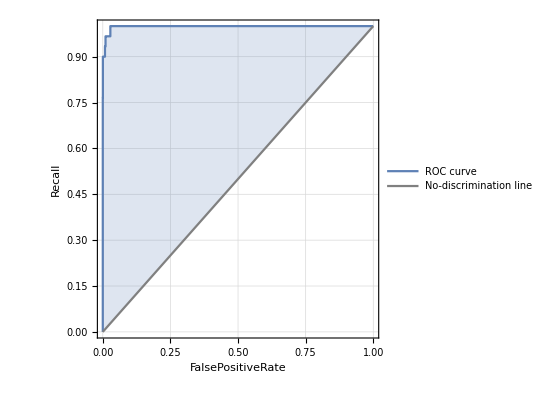
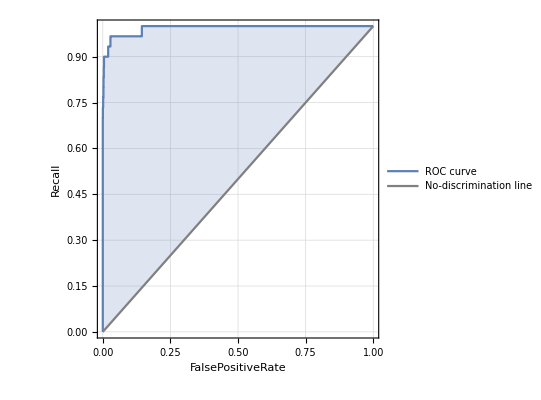
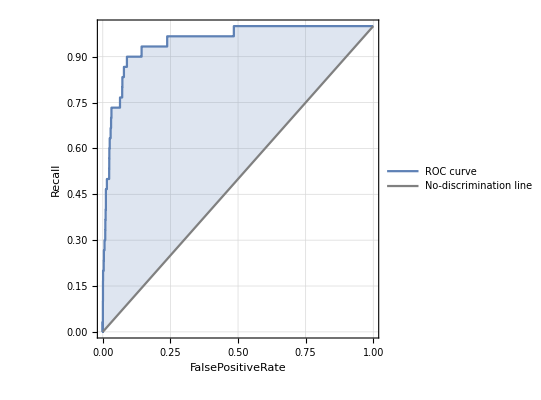
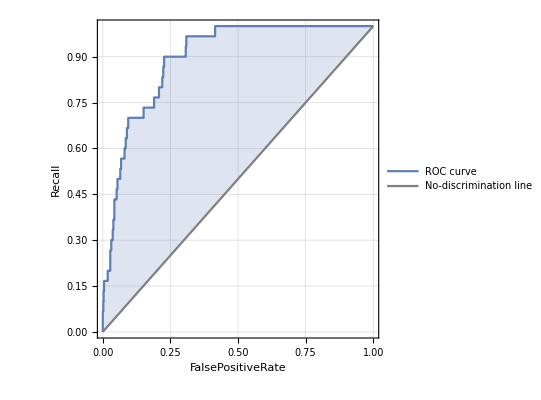
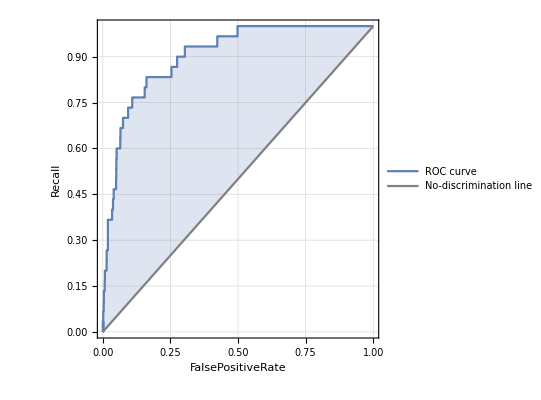
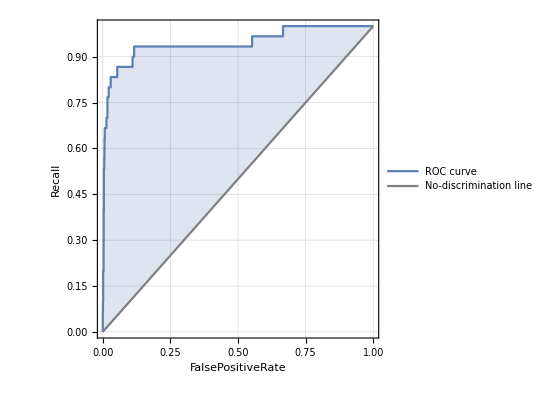
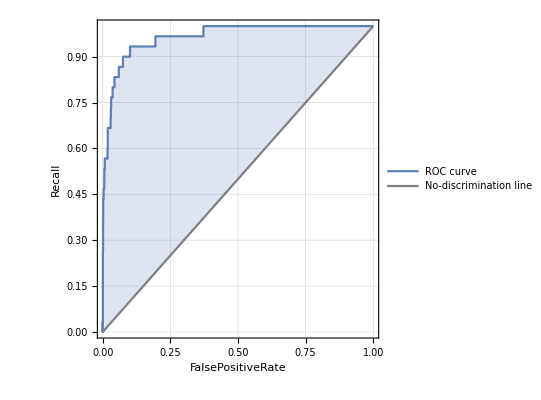
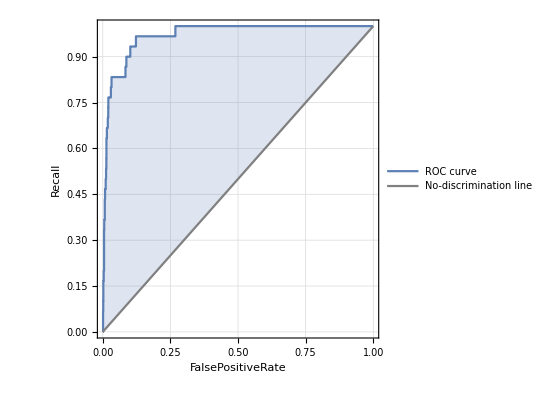
<|apple→-Graphics-,aquarium fish→-Graphics-,baby→-Graphics-,bear→-Graphics-,beaver→-Graphics-,bed→-Graphics-,bee→-Graphics-,beetle→-Graphics-,bicycle→-Graphics-,bottle→-Graphics-,bowl→-Graphics-,boy→-Graphics-,bridge→-Graphics-,bus→-Graphics-,butterfly→-Graphics-,camel→-Graphics-,can→-Graphics-,castle→-Graphics-,caterpillar→-Graphics-,cattle→-Graphics-,chair→-Graphics-,chimpanzee→-Graphics-,clock→-Graphics-,cloud→-Graphics-,cockroach→-Graphics-,computer keyboard→-Graphics-,couch→-Graphics-,crab→-Graphics-,crocodile→-Graphics-,cup→-Graphics-,dinosaur→-Graphics-,dolphin→-Graphics-,elephant→-Graphics-,flatfish→-Graphics-,forest→-Graphics-,fox→-Graphics-,girl→-Graphics-,hamster→-Graphics-,house→-Graphics-,kangaroo→-Graphics-,lamp→-Graphics-,lawn-mower→-Graphics-,leopard→-Graphics-,lion→-Graphics-,lizard→-Graphics-,lobster→-Graphics-,man→-Graphics-,maple tree→-Graphics-,motorcycle→-Graphics-,mountain→-Graphics-,mouse→-Graphics-,mushroom→-Graphics-,oak tree→-Graphics-,orange→-Graphics-,orchid→-Graphics-,otter→-Graphics-,palm tree→-Graphics-,pear→-Graphics-,pickup truck→-Graphics-,pine tree→-Graphics-,plain→-Graphics-,plate→-Graphics-,poppy→-Graphics-,porcupine→-Graphics-,possum→-Graphics-,rabbit→-Graphics-,raccoon→-Graphics-,ray→-Graphics-,road→-Graphics-,rocket→-Graphics-,rose→-Graphics-,sea→-Graphics-,seal→-Graphics-,shark→-Graphics-,shrew→-Graphics-,skunk→-Graphics-,skyscraper→-Graphics-,snail→-Graphics-,snake→-Graphics-,spider→-Graphics-,squirrel→-Graphics-,streetcar→-Graphics-,sunflower→-Graphics-,sweet pepper→-Graphics-,table→-Graphics-,tank→-Graphics-,telephone→-Graphics-,television→-Graphics-,tiger→-Graphics-,tractor→-Graphics-,train→-Graphics-,trout→-Graphics-,tulip→-Graphics-,turtle→-Graphics-,wardrobe→-Graphics-,whale→-Graphics-,willow tree→-Graphics-,wolf→-Graphics-,woman→-Graphics-,worm→-Graphics-|>

```mathematica
decisionMeasure["ROCCurve"]
```

#### Neural Networks

The ClassifierMeasurement function for neural networks:

```mathematica
neuralMeasure = ClassifierMeasurements[neuralNet,preProcessedTestData]
```

ClassifierMeasurementsObject[…]

Accuracy of the classifier:

```mathematica
neuralMeasure["Accuracy"]
```

0.576

Precision of each class in the dataset:

```mathematica
neuralMeasure["Precision"]
```

<|apple→0.756757,aquarium fish→0.916667,baby→0.472222,bear→0.416667,beaver→0.5,bed→0.807692,bee→0.46,beetle→0.228814,bicycle→0.888889,bottle→0.916667,bowl→0.4,boy→0.533333,bridge→0.489362,bus→0.769231,butterfly→0.6875,camel→0.73913,can→0.694444,castle→0.676471,caterpillar→0.490909,cattle→0.75,chair→1.,chimpanzee→0.777778,clock→0.866667,cloud→0.84,cockroach→1.,computer keyboard→0.787879,couch→0.541667,crab→0.387755,crocodile→0.576923,cup→0.473684,dinosaur→0.62963,dolphin→0.339286,elephant→0.566667,flatfish→0.585366,forest→0.5,fox→0.478261,girl→0.466667,hamster→0.530612,house→0.857143,kangaroo→0.428571,lamp→0.764706,lawn-mower→0.666667,leopard→0.611111,lion→0.436364,lizard→0.571429,lobster→0.722222,man→0.352941,maple tree→0.468085,motorcycle→0.756757,mountain→0.606061,mouse→0.470588,mushroom→0.866667,oak tree→0.52,orange→0.958333,orchid→0.7,otter→0.346154,palm tree→0.787879,pear→0.645161,pickup truck→0.534884,pine tree→0.486486,plain→0.846154,plate→0.875,poppy→0.833333,porcupine→0.8,possum→0.45,rabbit→0.285714,raccoon→0.388889,ray→0.705882,road→0.764706,rocket→0.621622,rose→1.,sea→0.583333,seal→0.347826,shark→0.6,shrew→0.222222,skunk→0.617647,skyscraper→0.875,snail→0.894737,snake→0.486486,spider→0.5,squirrel→0.652174,streetcar→0.512821,sunflower→0.96,sweet pepper→0.68,table→0.52,tank→0.789474,telephone→0.904762,television→0.6,tiger→0.857143,tractor→0.513514,train→0.636364,trout→0.857143,tulip→0.376812,turtle→0.475,wardrobe→0.727273,whale→0.566667,willow tree→0.571429,wolf→0.525,woman→0.8,worm→0.648649|>

Recall of each class in the dataset:

```mathematica
neuralMeasure["Recall"]
```

<|apple→0.933333,aquarium fish→0.733333,baby→0.566667,bear→0.333333,beaver→0.233333,bed→0.7,bee→0.766667,beetle→0.9,bicycle→0.533333,bottle→0.733333,bowl→0.466667,boy→0.266667,bridge→0.766667,bus→0.333333,butterfly→0.733333,camel→0.566667,can→0.833333,castle→0.766667,caterpillar→0.9,cattle→0.4,chair→0.466667,chimpanzee→0.7,clock→0.433333,cloud→0.7,cockroach→0.2,computer keyboard→0.866667,couch→0.433333,crab→0.633333,crocodile→0.5,cup→0.9,dinosaur→0.566667,dolphin→0.633333,elephant→0.566667,flatfish→0.8,forest→0.5,fox→0.733333,girl→0.233333,hamster→0.866667,house→0.2,kangaroo→0.3,lamp→0.433333,lawn-mower→0.733333,leopard→0.366667,lion→0.8,lizard→0.533333,lobster→0.433333,man→0.6,maple tree→0.733333,motorcycle→0.933333,mountain→0.666667,mouse→0.266667,mushroom→0.433333,oak tree→0.433333,orange→0.766667,orchid→0.7,otter→0.3,palm tree→0.866667,pear→0.666667,pickup truck→0.766667,pine tree→0.6,plain→0.733333,plate→0.466667,poppy→0.666667,porcupine→0.533333,possum→0.6,rabbit→0.4,raccoon→0.466667,ray→0.4,road→0.866667,rocket→0.766667,rose→0.266667,sea→0.538462,seal→0.235294,shark→0.1,shrew→0.4,skunk→0.7,skyscraper→0.7,snail→0.566667,snake→0.6,spider→0.166667,squirrel→0.5,streetcar→0.666667,sunflower→0.8,sweet pepper→0.566667,table→0.433333,tank→0.5,telephone→0.633333,television→0.9,tiger→0.4,tractor→0.633333,train→0.466667,trout→0.6,tulip→0.866667,turtle→0.633333,wardrobe→0.8,whale→0.566667,willow tree→0.133333,wolf→0.7,woman→0.133333,worm→0.8|>

ROC Curve for each class in the dataset:

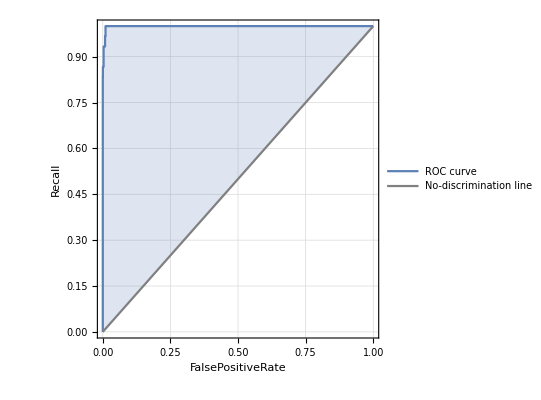
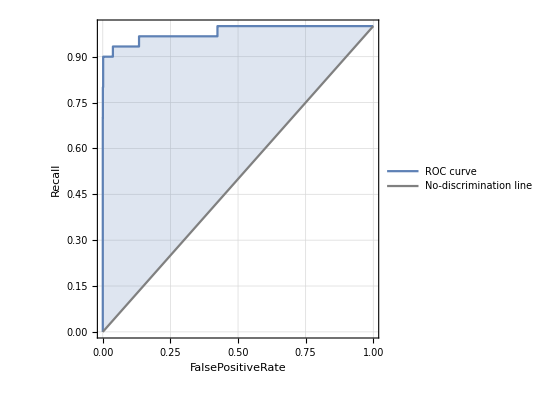
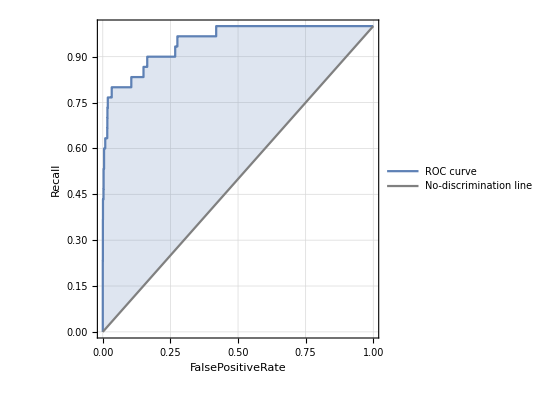
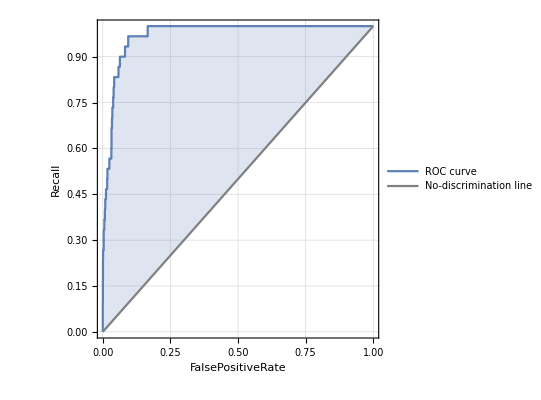
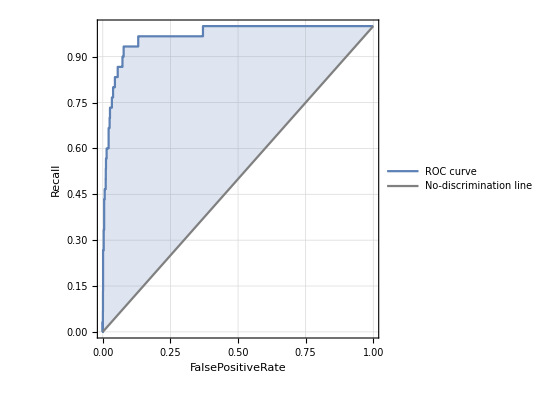
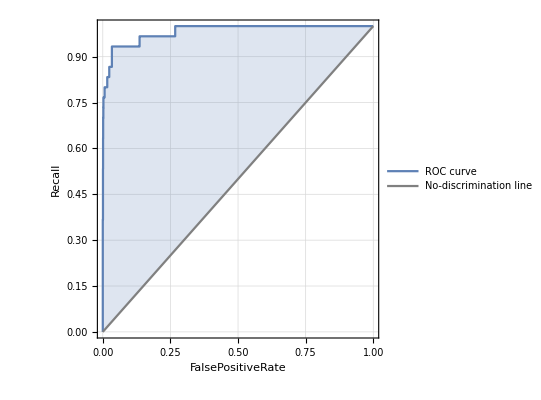
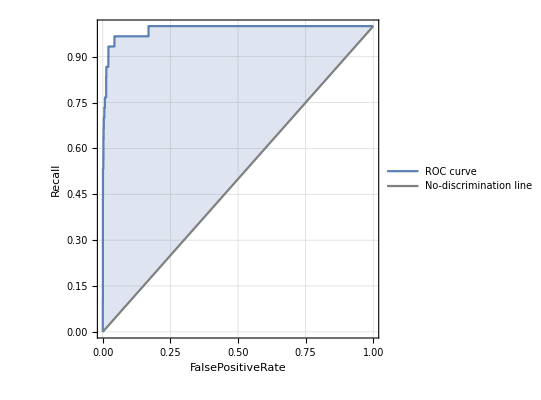
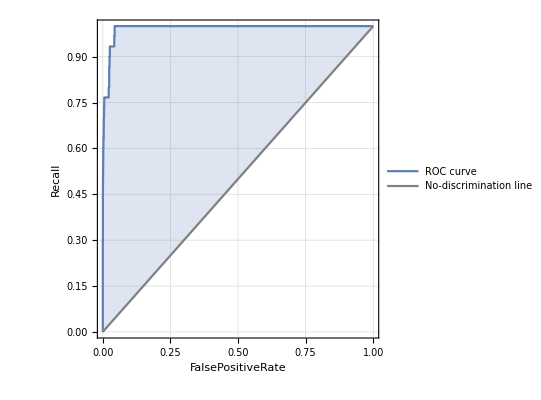
<|apple→-Graphics-,aquarium fish→-Graphics-,baby→-Graphics-,bear→-Graphics-,beaver→-Graphics-,bed→-Graphics-,bee→-Graphics-,beetle→-Graphics-,bicycle→-Graphics-,bottle→-Graphics-,bowl→-Graphics-,boy→-Graphics-,bridge→-Graphics-,bus→-Graphics-,butterfly→-Graphics-,camel→-Graphics-,can→-Graphics-,castle→-Graphics-,caterpillar→-Graphics-,cattle→-Graphics-,chair→-Graphics-,chimpanzee→-Graphics-,clock→-Graphics-,cloud→-Graphics-,cockroach→-Graphics-,computer keyboard→-Graphics-,couch→-Graphics-,crab→-Graphics-,crocodile→-Graphics-,cup→-Graphics-,dinosaur→-Graphics-,dolphin→-Graphics-,elephant→-Graphics-,flatfish→-Graphics-,forest→-Graphics-,fox→-Graphics-,girl→-Graphics-,hamster→-Graphics-,house→-Graphics-,kangaroo→-Graphics-,lamp→-Graphics-,lawn-mower→-Graphics-,leopard→-Graphics-,lion→-Graphics-,lizard→-Graphics-,lobster→-Graphics-,man→-Graphics-,maple tree→-Graphics-,motorcycle→-Graphics-,mountain→-Graphics-,mouse→-Graphics-,mushroom→-Graphics-,oak tree→-Graphics-,orange→-Graphics-,orchid→-Graphics-,otter→-Graphics-,palm tree→-Graphics-,pear→-Graphics-,pickup truck→-Graphics-,pine tree→-Graphics-,plain→-Graphics-,plate→-Graphics-,poppy→-Graphics-,porcupine→-Graphics-,possum→-Graphics-,rabbit→-Graphics-,raccoon→-Graphics-,ray→-Graphics-,road→-Graphics-,rocket→-Graphics-,rose→-Graphics-,sea→-Graphics-,seal→-Graphics-,shark→-Graphics-,shrew→-Graphics-,skunk→-Graphics-,skyscraper→-Graphics-,snail→-Graphics-,snake→-Graphics-,spider→-Graphics-,squirrel→-Graphics-,streetcar→-Graphics-,sunflower→-Graphics-,sweet pepper→-Graphics-,table→-Graphics-,tank→-Graphics-,telephone→-Graphics-,television→-Graphics-,tiger→-Graphics-,tractor→-Graphics-,train→-Graphics-,trout→-Graphics-,tulip→-Graphics-,turtle→-Graphics-,wardrobe→-Graphics-,whale→-Graphics-,willow tree→-Graphics-,wolf→-Graphics-,woman→-Graphics-,worm→-Graphics-|>

```mathematica
neuralMeasure["ROCCurve"]
```

#### Support Vector Machine:

The ClassifierMeasurement function for support vector machine:

```mathematica
svmMeasure = ClassifierMeasurements[supportVector,preProcessedTestData]
```

ClassifierMeasurementsObject[…]

Accuracy of the classifier:

```mathematica
svmMeasure["Accuracy"]
```

0.634667

Precision of each class in the dataset:

```mathematica
svmMeasure["Precision"]
```

<|apple→1.,aquarium fish→0.884615,baby→0.387755,bear→0.4,beaver→0.727273,bed→0.692308,bee→0.733333,beetle→0.645161,bicycle→0.862069,bottle→0.866667,bowl→0.483871,boy→0.5,bridge→0.68,bus→0.75,butterfly→0.818182,camel→0.695652,can→0.862069,castle→0.833333,caterpillar→0.8,cattle→0.607143,chair→0.78125,chimpanzee→0.647059,clock→0.913043,cloud→0.75,cockroach→0.8,computer keyboard→0.928571,couch→0.515152,crab→0.692308,crocodile→0.457143,cup→0.787879,dinosaur→0.617647,dolphin→0.567568,elephant→0.566667,flatfish→0.589744,forest→0.48,fox→0.555556,girl→0.304348,hamster→0.657143,house→0.571429,kangaroo→0.666667,lamp→0.452381,lawn-mower→0.709677,leopard→0.327273,lion→0.657143,lizard→0.515152,lobster→0.545455,man→0.473684,maple tree→0.571429,motorcycle→0.931034,mountain→0.782609,mouse→0.578947,mushroom→0.692308,oak tree→0.477273,orange→0.90625,orchid→0.657895,otter→0.194444,palm tree→0.83871,pear→0.628571,pickup truck→0.777778,pine tree→0.517241,plain→0.88,plate→0.714286,poppy→0.7,porcupine→0.681818,possum→0.388889,rabbit→0.470588,raccoon→0.5,ray→0.62069,road→0.827586,rocket→0.866667,rose→0.862069,sea→0.608696,seal→0.268293,shark→0.545455,shrew→0.423077,skunk→0.645161,skyscraper→0.851852,snail→0.708333,snake→0.477273,spider→0.585366,squirrel→0.5,streetcar→0.488372,sunflower→0.875,sweet pepper→0.863636,table→0.4375,tank→0.894737,telephone→0.807692,television→0.722222,tiger→0.642857,tractor→0.703704,train→0.642857,trout→0.7,tulip→0.488372,turtle→0.607143,wardrobe→0.735294,whale→0.592593,willow tree→0.363636,wolf→0.606061,woman→0.56,worm→0.714286|>

Recall of each class in the dataset:

```mathematica
svmMeasure["Recall"]
```

<|apple→0.866667,aquarium fish→0.766667,baby→0.633333,bear→0.4,beaver→0.266667,bed→0.6,bee→0.733333,beetle→0.666667,bicycle→0.833333,bottle→0.866667,bowl→0.5,boy→0.433333,bridge→0.566667,bus→0.5,butterfly→0.6,camel→0.533333,can→0.833333,castle→0.833333,caterpillar→0.8,cattle→0.566667,chair→0.833333,chimpanzee→0.733333,clock→0.7,cloud→0.7,cockroach→0.666667,computer keyboard→0.866667,couch→0.566667,crab→0.6,crocodile→0.533333,cup→0.866667,dinosaur→0.7,dolphin→0.7,elephant→0.566667,flatfish→0.766667,forest→0.4,fox→0.833333,girl→0.233333,hamster→0.766667,house→0.533333,kangaroo→0.466667,lamp→0.633333,lawn-mower→0.733333,leopard→0.6,lion→0.766667,lizard→0.566667,lobster→0.6,man→0.3,maple tree→0.533333,motorcycle→0.9,mountain→0.6,mouse→0.366667,mushroom→0.6,oak tree→0.7,orange→0.966667,orchid→0.833333,otter→0.233333,palm tree→0.866667,pear→0.733333,pickup truck→0.7,pine tree→0.5,plain→0.733333,plate→0.666667,poppy→0.7,porcupine→0.5,possum→0.466667,rabbit→0.266667,raccoon→0.5,ray→0.6,road→0.8,rocket→0.866667,rose→0.833333,sea→0.538462,seal→0.323529,shark→0.6,shrew→0.366667,skunk→0.666667,skyscraper→0.766667,snail→0.566667,snake→0.7,spider→0.8,squirrel→0.4,streetcar→0.7,sunflower→0.933333,sweet pepper→0.633333,table→0.466667,tank→0.566667,telephone→0.7,television→0.866667,tiger→0.6,tractor→0.633333,train→0.6,trout→0.7,tulip→0.7,turtle→0.566667,wardrobe→0.833333,whale→0.533333,willow tree→0.266667,wolf→0.666667,woman→0.466667,worm→0.833333|>

ROC Curve for each class in the dataset:

```mathematica
svmMeasure["ROCCurve"]
```

<|apple→-Graphics-,aquarium fish→-Graphics-,baby→-Graphics-,bear→-Graphics-,beaver→-Graphics-,bed→-Graphics-,bee→-Graphics-,beetle→-Graphics-,bicycle→-Graphics-,bottle→-Graphics-,bowl→-Graphics-,boy→-Graphics-,bridge→-Graphics-,bus→-Graphics-,butterfly→-Graphics-,camel→-Graphics-,can→-Graphics-,castle→-Graphics-,caterpillar→-Graphics-,cattle→-Graphics-,chair→-Graphics-,chimpanzee→-Graphics-,clock→-Graphics-,cloud→-Graphics-,cockroach→-Graphics-,computer keyboard→-Graphics-,couch→-Graphics-,crab→-Graphics-,crocodile→-Graphics-,cup→-Graphics-,dinosaur→-Graphics-,dolphin→-Graphics-,elephant→-Graphics-,flatfish→-Graphics-,forest→-Graphics-,fox→-Graphics-,girl→-Graphics-,hamster→-Graphics-,house→-Graphics-,kangaroo→-Graphics-,lamp→-Graphics-,lawn-mower→-Graphics-,leopard→-Graphics-,lion→-Graphics-,lizard→-Graphics-,lobster→-Graphics-,man→-Graphics-,maple tree→-Graphics-,motorcycle→-Graphics-,mountain→-Graphics-,mouse→-Graphics-,mushroom→-Graphics-,oak tree→-Graphics-,orange→-Graphics-,orchid→-Graphics-,otter→-Graphics-,palm tree→-Graphics-,pear→-Graphics-,pickup truck→-Graphics-,pine tree→-Graphics-,plain→-Graphics-,plate→-Graphics-,poppy→-Graphics-,porcupine→-Graphics-,possum→-Graphics-,rabbit→-Graphics-,raccoon→-Graphics-,ray→-Graphics-,road→-Graphics-,rocket→-Graphics-,rose→-Graphics-,sea→-Graphics-,seal→-Graphics-,shark→-Graphics-,shrew→-Graphics-,skunk→-Graphics-,skyscraper→-Graphics-,snail→-Graphics-,snake→-Graphics-,spider→-Graphics-,squirrel→-Graphics-,streetcar→-Graphics-,sunflower→-Graphics-,sweet pepper→-Graphics-,table→-Graphics-,tank→-Graphics-,telephone→-Graphics-,television→-Graphics-,tiger→-Graphics-,tractor→-Graphics-,train→-Graphics-,trout→-Graphics-,tulip→-Graphics-,turtle→-Graphics-,wardrobe→-Graphics-,whale→-Graphics-,willow tree→-Graphics-,wolf→-Graphics-,woman→-Graphics-,worm→-Graphics-|>

## Conclusion

In this project, I have performed three classification techniques to determine which is the best classifier for the above dataset.From the information gathered I see that the potential of Support Vector Machines in the problems of image classification. It appears that unlike the other learning techniques, SVM gives excellent results for image classification.Thus this result can be used for similar image classification datasets.